```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
data = Import["../../runs/Trials/N7K9/30552874.dat"];
```

```mathematica
data = data[[1;;10000]];
```

```mathematica
changeNK[7, 9];
```

```mathematica
cdata = cMat[data];
```

```mathematica
eigdata = Eigenvalues/@cdata[[All, 5]] //Flatten;
```

```mathematica
plt = Histogram[eigdata,100,PDF,PlotLabel->"Distribution of eigenvalues of a matrix for N7 K9",AxesLabel->{Eigenvalues}];
```

```mathematica
EigenvaluesContinuous[cdata_, $tSize_] := Module[{goodlist, eiglist}, (
goodlist = {{cdata[[1, 1]], Eigenvalues@cdata[[1, 2]]}};
eiglist = {Eigenvalues@cdata[[1, 2]]};
Module[{e, sortede, f}, Do[(
e = Eigenvalues[cdata[[t, 2]]];

sortede = Table[(
f = Quiet[Interpolation[eiglist[[All, m]]][Length[eiglist] + 1]];
First@Nearest[e, f]
), {m, 1, Length[e]}];

If[Length[eiglist] >= $tSize, 
eiglist = Append[eiglist[[2;;]], sortede], 
AppendTo[eiglist, sortede]
];

AppendTo[goodlist, {cdata[[t, 1]], sortede}];
), {t, 2, Length[cdata]}]];
goodlist
)];
```

```mathematica
ee = EigenvaluesContinuous[cdata, 50];
eold = ListPlot[Thread[Table[{#[[1]], y}, {y, #[[2]]}]&/@ee], PlotRange->{{24.8,25.5}, All}, PlotStyle->PointSize[0.02]];
```

```mathematica
Length[cdata]
```

10000

```mathematica
Eigenvalues@cdata[[1,2]]
```

{-0.404923,0.390063,-0.252105,0.211463,-0.177669,0.138851,0.0943207}

```mathematica
Table[{i,j},{i,1,3},{j,11,18}]
```

{{{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18}},{{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18}},{{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18}}}

```mathematica
(Eigenvalues@cdata[[2,2]])
```

{-0.403032,0.387805,-0.251079,0.210531,-0.176931,0.138443,0.0942627}

```mathematica
Table[(Eigenvalues@cdata[[3,2]])[[First@Nearest[Eigenvalues@cdata[[3,2]]-(Eigenvalues@cdata[[2,2]])[[i]] ->"Index",((Eigenvalues@cdata[[2,2]])[[i]]-(Eigenvalues@cdata[[1,2]])[[i]])]]],{i,1,$N}]
```

{-0.397432,0.381122,-0.248037,0.207776,-0.174737,0.137234,0.0940743}

```mathematica
Eigenvalues@cdata[[3,2]]
```

{-0.397432,0.381122,-0.248037,0.207776,-0.174737,0.137234,0.0940743}

```mathematica
goodlist ={};
Module[{}, 

Do[(
tplus1 = (Eigenvalues@cdata[[t+1,2]]);
teigs = (Eigenvalues@cdata[[t,2]]);
tminus1 = (Eigenvalues@cdata[[t-1,2]]);
sortede = Table[tplus1[[First@Nearest[tplus1-teigs[[i]] ->"Index",(teigs[[i]]-tminus1[[i]])]]],{i,1,$N}];

AppendTo[goodlist, {cdata[[t+1, 1]], sortede}];
), {t, 5,6}]];
```

```mathematica
Sqrt[(tplus1[[2]]-teigs[[2]])^2]
```

0.0205601

```mathematica
Sqrt[(tminus1[[2]]-teigs[[2]])^2]
```

0.017875

```mathematica
Eigenvalues@cdata[[1,2]]
```

{-0.404923,0.390063,-0.252105,0.211463,-0.177669,0.138851,0.0943207}

```mathematica
Eigenvalues@cdata[[2,2]]
```

{-0.403032,0.387805,-0.251079,0.210531,-0.176931,0.138443,0.0942627}

```mathematica
({1,2,3}-{3,4,5})^2
```

{4,4,4}

```mathematica
goodlist
```

{{0.5,{-0.361044,0.337779,-0.228106,0.190107,-0.160252,0.129397,0.0921192}},{0.6,{-0.34373,0.317219,-0.21852,0.18187,-0.153211,0.125765,0.0906076}}}

```mathematica
EigenvaluesJoin[cdata_,beta_] := Module[{goodlist, eiglist}, (
goodlist = {{cdata[[1, 1]], Eigenvalues@cdata[[1, 2]]},{cdata[[2, 1]], Eigenvalues@cdata[[2, 2]]}};
Module[{sortede, tplus1,teigs,tminus1,indx, score,scrval,slopetplus1,slopeteigs}, 

Do[(
tplus1 = (Eigenvalues@cdata[[t+1,2]]);
teigs = (Eigenvalues@cdata[[t,2]]);
tminus1 = (Eigenvalues@cdata[[t-1,2]]);
sortede = {};
Do[(
score={};

slopetplus1 = tplus1-teigs[[i]];
slopeteigs =teigs[[i]]-tminus1;
Do[(
scrval = Sqrt[(tplus1[[j]]-teigs[[i]])^2+beta(slopetplus1[[j]]-slopeteigs[[i]])^2 ] ;
AppendTo[score , scrval];),{j,1,$N}];
indx = First@Nearest[score->"Index",Sqrt[(teigs[[i]]-tminus1[[i]])^2] ];
AppendTo[sortede , tplus1[[indx]]];

),{i,1,$N}];
AppendTo[goodlist, {cdata[[t+1, 1]], sortede}];
), {t, 2,Length[cdata]-1}]];
goodlist
)];
```

```mathematica
eesmooth = EigenvaluesJoin[cdata,0]
```

```mathematica
pltsmooth = ListPlot[Thread[Table[{#[[1]], y}, {y, #[[2]]}]&/@eesmooth], PlotRange->{{24.8,25.5}, All}, PlotStyle->PointSize[0.02]];
```

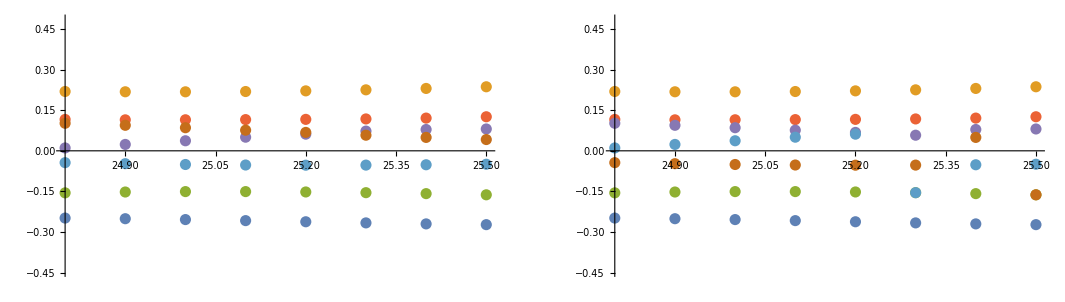

```mathematica
GraphicsRow[{eold,pltsmooth}]
```